1

2

3

4

5

6

7

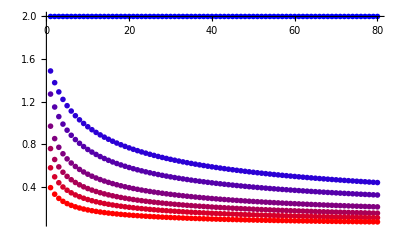

```mathematica
F[n_,λ_]:=NIntegrate[x^(2n)Exp[-x^2/2-λ x^4/4],{x,-∞,+∞}];
nmax=80;
λ0s={0.0,0.1,0.2,0.5,1.0,2.0,5.0};
nλ=Length[λ0s];
GrS={};
For[iλ=1,iλ≤nλ,iλ++,
Print[iλ];
λ0=λ0s[[iλ]];
r=(iλ-1)/(nλ-1);
FT1=Table[F[n,λ0],{n,1,nmax+1}];
FT=Table[FT1[[n+1]]/((n+0.5) FT1[[n]]),{n,1,nmax}];
Gr=ListPlot[FT,PlotRange->All,PlotStyle->{PointSize[0.01],RGBColor[r,0.0,1-r]}];
AppendTo[GrS,Gr];
];
Show[GrS]
```

```mathematica
(* Fun with the Vandermonde *)
NC=4;
VDM=Product[If[i>=j,1,(Symbol["x"<>ToString[i]]- Symbol["x"<>ToString[j]])],{i,1,NC},{j,1,NC}]
FullSimplify[VDM]
Expand[VDM]
MatrixForm[MonomialList[VDM]]
```

(x1-x2) (x1-x3) (x2-x3) (x1-x4) (x2-x4) (x3-x4)

(x1-x2) (x1-x3) (x2-x3) (x1-x4) (x2-x4) (x3-x4)

x1^3 x2^2 x3-x1^2 x2^3 x3-x1^3 x2 x3^2+x1 x2^3 x3^2+x1^2 x2 x3^3-x1 x2^2 x3^3-x1^3 x2^2 x4+x1^2 x2^3 x4+x1^3 x3^2 x4-x2^3 x3^2 x4-x1^2 x3^3 x4+x2^2 x3^3 x4+x1^3 x2 x4^2-x1 x2^3 x4^2-x1^3 x3 x4^2+x2^3 x3 x4^2+x1 x3^3 x4^2-x2 x3^3 x4^2-x1^2 x2 x4^3+x1 x2^2 x4^3+x1^2 x3 x4^3-x2^2 x3 x4^3-x1 x3^2 x4^3+x2 x3^2 x4^3

(x1^3 x2^2 x3
-x1^3 x2^2 x4
-x1^3 x2 x3^2
x1^3 x2 x4^2
x1^3 x3^2 x4
-x1^3 x3 x4^2
-x1^2 x2^3 x3
x1^2 x2^3 x4
x1^2 x2 x3^3
-x1^2 x2 x4^3
-x1^2 x3^3 x4
x1^2 x3 x4^3
x1 x2^3 x3^2
-x1 x2^3 x4^2
-x1 x2^2 x3^3
x1 x2^2 x4^3
x1 x3^3 x4^2
-x1 x3^2 x4^3
-x2^3 x3^2 x4
x2^3 x3 x4^2
x2^2 x3^3 x4
-x2^2 x3 x4^3
-x2 x3^3 x4^2
x2 x3^2 x4^3)

```mathematica
Polynomial
```